# wbBrancUNICond wbBrancUNINec1Cond

functions that filter the couplings according to the perturbative unitarity conditions of Branco's model.

## Documentation

### Usage

wbBrancUNICond[list, M_max ]

Filter the couplings according to the UNI conditions given in Refs. [1, 2]. The eigenvalues of the scattering matrix are bounded by a quantity M_max, which is typically taken to be 8π. Return: False | True.

wbBrancUNINec1Cond[list, M_max]

This function is identical to wbBrancParRndUni, but includes additional filtering based on the necessary BFB conditions for the 2HDM (NCL1). Return: False | True.

## Examples

To test usage examples make sure the package has been loaded:

```mathematica
wbLoadBinaries=True;(*wpCompTarget="C";*)
NotebookEvaluate[FileNameJoin[{ParentDirectory@NotebookDirectory[EvaluationNotebook[]],"StableWein.nb"}]]
```

### Basic Examples

Generate a set of couplings within the specified range and evaluate the UNI conditions:

```mathematica
couplSet=wbBrancParRndUniNec[]
```

{7.85485,6.22308,4.15547,-4.52431,-2.17519,8.44255,12.2324,-0.255966,12.6664,-3.54393,7.52346,6.99345}

```mathematica
wbBrancUNICond[couplSet,8 π]
wbBrancUNINec1Cond[couplSet,8 π]
```

False

False

Only a very small fraction of points satisfy the UNI conditions, or both the UNI and necessary BFB conditions, when the parameters are generated within the same ranges:

```mathematica
data=ParallelTable[wbBrancParRnd[16],{10^7}];
dataUNI1=Pick[data,ParallelMap[wbBrancUNICond[#, 8 π]&,data]];
dataUNI2=Pick[data,ParallelMap[wbBrancUNINec1Cond[#, 8 π]&,data]];
Length/@{dataUNI1,dataUNI2}
PercentForm/@N[%/Length[data]]
```

{1249,5}

{0.01249%,0.00005%}

Generating points with function wbBrancParRndUni increases the probability of selecting a point that satisfies the UNI conditions:

```mathematica
data=ParallelTable[wbBrancParRndUni[],{10^7}];
dataUNI1=Pick[data,ParallelMap[wbBrancUNICond[#, 8 π]&,data]];
dataUNI2=Pick[data,ParallelMap[wbBrancUNINec1Cond[#, 8 π]&,data]];
Length/@{dataUNI1,dataUNI2}
PercentForm/@N[%/Length[data]]
```

{40446,101}

{0.4045%,0.00101%}

While function wbBrancParRndUniNec even more increase the probability of selecting a point that satisfies the UNI + NCL1 conditions:

```mathematica
data=ParallelTable[wbBrancParRndUniNec[],{10^7}];
dataUNI1=Pick[data,ParallelMap[wbBrancUNICond[#, 8 π]&,data]];
dataUNI2=Pick[data,ParallelMap[wbBrancUNINec1Cond[#, 8 π]&,data]];
Length/@{dataUNI1,dataUNI2}
PercentForm/@N[%/Length[data]]
```

{70420,2639}

{0.7042%,0.02639%}

### Scope

Couplings generated with appropriate UNI functions:

```mathematica
dataUNI1=ParallelTable[testT=False; While[testT==False,paramT=wbBrancParRndUni[]; testT=wbBrancUNICond[paramT,8 π]]; paramT,{10^6}];
dataUNI2=ParallelTable[testT=False; While[testT==False,paramT=wbBrancParRndUniNec[]; testT=wbBrancUNINec1Cond[paramT,8 π]]; paramT,{10^6}];
```

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUNI1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUNI2),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"wbBrancUNICond[8π]","wbBrancUNINec1Cond[8π]"},{table1,table2}}]);
Grid[{%},Spacings->{4, 0}]
```

wbBrancUNICond[8π]
 | Min | Max
a_1 | -8.37 | 8.37
a_2 | -8.37 | 8.37
a_3 | -8.37 | 8.37
b_1 | -16.23 | 16.32
b_2 | -16.31 | 16.26
b_3 | -16.36 | 16.2
c_1 | -16.7 | 16.62
c_2 | -16.64 | 16.64
c_3 | -16.58 | 16.61
d_1 | -8.37 | 8.36
d_2 | -8.37 | 8.36
d_3 | -8.37 | 8.36 | wbBrancUNINec1Cond[8π]
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.38
b_1 | -7.82 | 15.97
b_2 | -7.75 | 15.94
b_3 | -7.91 | 15.73
c_1 | -15.75 | 15.71
c_2 | -15.74 | 15.78
c_3 | -15.84 | 15.68
d_1 | -8.26 | 8.2
d_2 | -8.07 | 8.06
d_3 | -8.24 | 8.24

Distribution of the couplings filtered with function wbBrancUNICond (green area) and function wbBrancUNINec1Cond with additional necessary BFB conditions for the 2HDM (blue area):

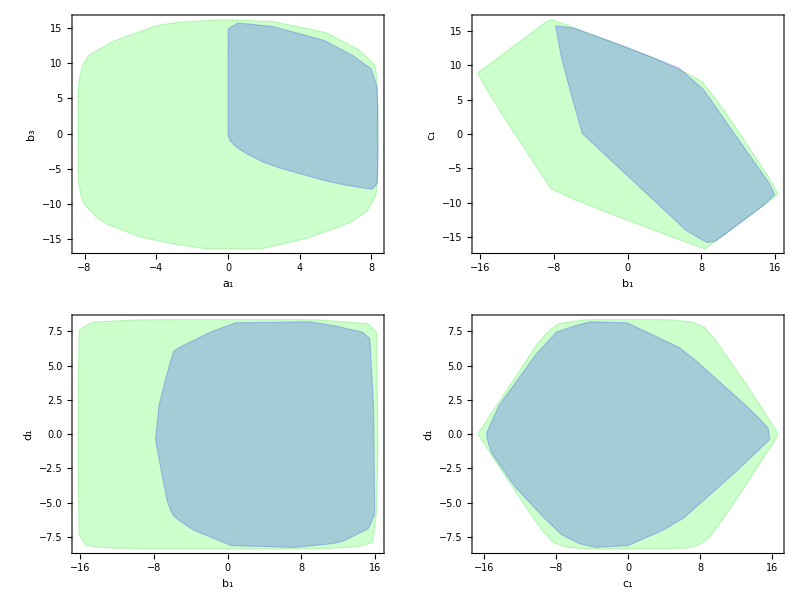

```mathematica
Table[Show[{ConvexHullMesh[dataUNI1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0.2,Green]}],ConvexHullMesh[dataUNI2[[;;,xx]],MeshCellStyle->{1->{Blue},2->Opacity[0.2,Blue]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

### Options

## Source & Additional Information

### Related Symbols

wbBrancParRnd ▪ wbBrancParRndNec ▪ wbBrancParRndUni ▪ wbBrancParRndUniNec  ▪ wbBrancSufCond  ▪ wbBrancNecCond1  ▪ wbBrancNecCond2  ▪ wbBrancNecCond3  ▪ wbBrancUniBFBcheck

### References

[1] M.P. Bento, J.C. Romao and J.P. Silva, Unitarity bounds for all symmetry-constrained 3HDMs, JHEP 08 (2022), 273, https://doi.org/10.1007/JHEP08(2022)273 [arXiv:2204.13130 [hep-ph]].

[2] S. Moretti and K. Yagyu, Constraints on Parameter Space from Perturbative Unitarity in Models with Three Scalar Doublets, Phys. Rev. D 91 (2015), 055022, https://doi.org/10.1103/PhysRevD.91.055022 [arXiv:1501.06544 [hep-ph]].